#### Problem 7.5.24ab

```mathematica
f[A_,B_,t_]:=-A*Exp[-t]+B*Exp[-2t]
```

```mathematica
g[A_,B_,t_]:=2*A*Exp[-t]+2*B*Exp[-2t]
```

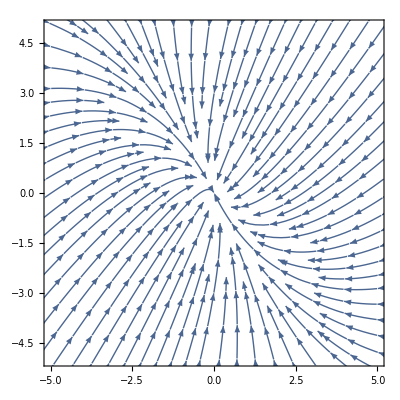
-Graphics--Graphics-

```mathematica
Overlay[{ParametricPlot[{f[-0.25,1.75,t],g[-0.25,1.75,t]},{t,-25,23}, PlotRange->{{-5.4,5},{-5,4.9}}],StreamPlot[{(-3/2)*x-(1/4)y,-x-(3/2)y},{x,-6,6},{y,-6,6}, PlotRange->{{-5,5},{-5,5}}]}]
```

```mathematica
Solve[{2==-A+B, 3==2*A+2*B}, {A,B}]
```

{{A→-1/4,B→7/4}}

#### c

```mathematica
Plot[{Callout[f[-0.25,1.75,t],"x1",{0.5,0.5}],Callout[g[-0.25,1.75,t],"x2", {0.5,2}]},{t,-1,5}, PlotRange-> {{0,3},{0,3}}]
```

-Graphics-

#### Problem 7.5.26ab

```mathematica
h[A_,B_,t_]:=-A*Exp[-t]+B*Exp[2t]
```

```mathematica
k[A_,B_,t_]:=2*A*Exp[-t]+2*B*Exp[2t]
```

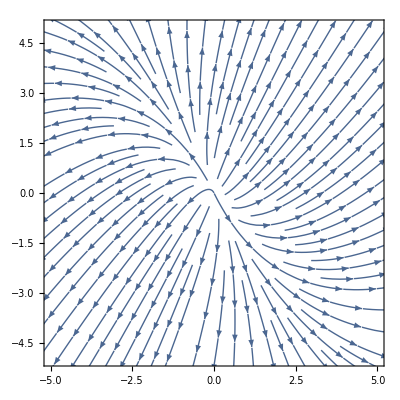
-Graphics--Graphics-

```mathematica
Overlay[{ParametricPlot[{h[-0.25,1.75,t],k[-0.25,1.75,t]},{t,-25,23}, PlotRange->{{-5.4,5},{-5,4.9}}],StreamPlot[{(3/2)*x+(1/4)y,x+(3/2)y},{x,-6,6},{y,-6,6}, PlotRange->{{-5,5},{-5,5}}]}]
```

```mathematica
Solve[{2==-A+B,3==2A+2B},{A,B}]
```

{{A→-1/4,B→7/4}}

#### C

```mathematica
Plot[{Callout[h[-0.25,1.75,t],"x1",{1,10}],Callout[k[-0.25,1.75,t],"x2", {1,30}]},{t,-1,5}, PlotRange-> {{0,2},{0,50}}]
```

-Graphics-

#### 7.6.3b

```mathematica
Unprotect[N]
```

{}

```mathematica
Clear[N]
```

```mathematica
M1[A_,B_,t_]:=A*-5* Cos[t]+B*-5*Sin[t]
```

```mathematica
M2[A_,B_,t_]:=A*(-2*Cos[t] -Sin[t])+B*(Cos[t]-2*Sin[t])
```

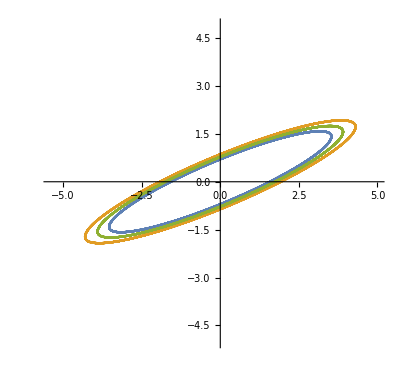
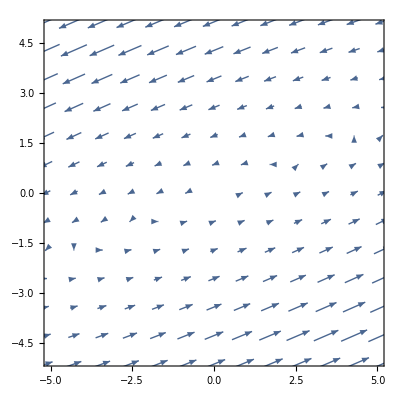

```mathematica
Overlay[{ParametricPlot[{{M1[.5,.5,t],M2[.5,.5,t]},{M1[-.7,.5,t],M2[-.7,.5,t]},{M1[.5,-.6,t],M2[.5,-.6,t]}},{t,-25,23}, PlotRange->{{-5.4,5},{-5,4.9}}],VectorPlot[{2*x-5y,x-2y},{x,-6,6},{y,-6,6}, PlotRange->{{-5,5},{-5,5}}]}]
```

#### 7.6.5b

```mathematica
N1[A_,B_,t_]:=Exp[-t]*(A*- Cos[t]+B*-Sin[t])
```

```mathematica
N2[A_,B_,t_]:=Exp[-t]*(A*(-2*Cos[t]- Sin[t])+B*(Cos[t]-2*Sin[t]))
```

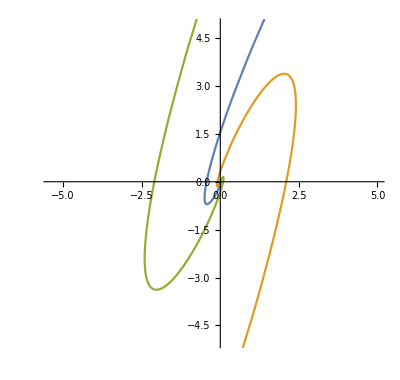
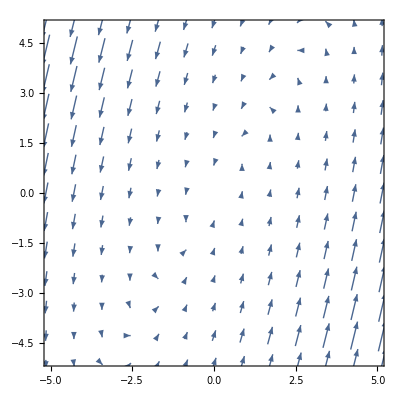

```mathematica
Overlay[{ParametricPlot[{{N1[.5,.5,t],N2[.5,.5,t]},{N1[-.5,.5,t],N2[-.5,.5,t]},{N1[.5,-.5,t],N2[.5,-.5,t]}},{t,-25,23}, PlotRange->{{-5.4,5},{-5,4.9}}],VectorPlot[{x-y,5x-3y},{x,-6,6},{y,-6,6}, PlotRange->{{-5,5},{-5,5}}]}]
```

#### 9.6.9

```mathematica
O1[A_,B_,t_]:=Exp[-t]*(A*- 5*Cos[t]+B*-5*Sin[t])
```

```mathematica
O2[A_,B_,t_]:=Exp[-t]*(A*(2Cos[t]+Sin[t])+B*(-Cos[t]+2*Sin[t]))
```

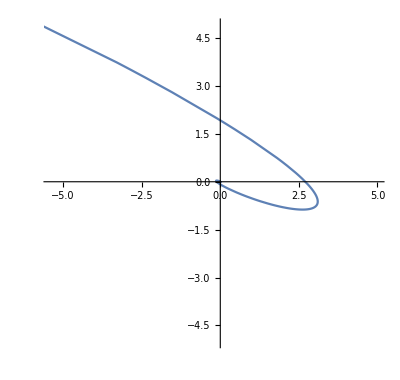
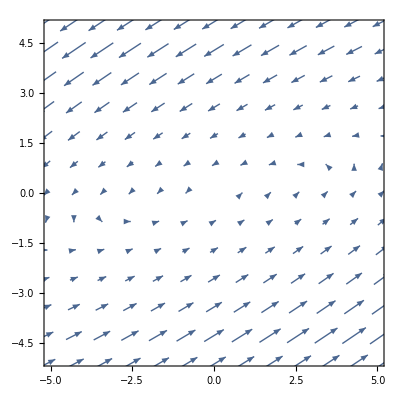

```mathematica
Overlay[{ParametricPlot[{O1[-0.4,-1.4,t],O2[-.4,-1.4,t]},{t,-25,23}, PlotRange->{{-5.4,5},{-5,4.9}}],VectorPlot[{x-5y,x-3y},{x,-6,6},{y,-6,6}, PlotRange->{{-5,5},{-5,5}}]}]
```